```mathematica
Remove["Global`*"];
ClearAll["Global`*"];
```

```mathematica
Ndof=1+n+n(n+1)/2//.{n->m+1,m->3}//FullSimplify
```

15

```mathematica
pc[T_,μB_]:=Sum[Subscript[a, 2i,2j] T^(2i)μB^(2j)KroneckerDelta[2(i+j),4],{i,0,2},{j,0,2}];
pnonc[T_,μB_]:=T^4 Sum[Subscript[b, 2i,2j][T](μB/T)^(2i),{i,0,2}];
(*S[T_,μB_]:=1/2(1+Tanh[g(T^2+d μB^2-f)]);*)
p[T_,μB_]:=pc[T,μB]S[T,μB]+pnonc[T,μB](1-S[T,μB]);
s[T_,μB_]:=Evaluate[D[p[T,μB], T]];
ρB[T_,μB_]:=Evaluate[D[p[T,μB], μB]];
e[T_,μB_]:=T s[T,μB]+μB ρB[T,μB]-p[T,μB];
χTT[T_,μB_]:=Evaluate[D[p[T,μB], T,T]];
χTμB[T_,μB_]:=Evaluate[D[p[T,μB], T,μB]];
χμBμB[T_,μB_]:=Evaluate[D[p[T,μB], μB,μB]];
```

```mathematica
e[T,μB]//FullSimplify

p[T,μB]//FullSimplify
s[T,μB]//FullSimplify
ρB[T,μB]//FullSimplify
χTT[T,μB]//FullSimplify
χTμB[T,μB]//FullSimplify
χμBμB[T,μB]//FullSimplify
```

-b_(0,0)+μB^2 b_(2,0)+T^2 (b_(0,2)+3 T^2 b_(0,4)+3 μB^2 b_(2,2))+3 μB^4 b_(4,0)

b_(0,0)+μB^2 b_(2,0)+T^2 (b_(0,2)+T^2 b_(0,4)+μB^2 b_(2,2))+μB^4 b_(4,0)

2 T (b_(0,2)+2 T^2 b_(0,4)+μB^2 b_(2,2))

2 μB (b_(2,0)+T^2 b_(2,2)+2 μB^2 b_(4,0))

2 (b_(0,2)+6 T^2 b_(0,4)+μB^2 b_(2,2))

4 T μB b_(2,2)

2 (b_(2,0)+T^2 b_(2,2)+6 μB^2 b_(4,0))

```mathematica
T^4 Sum[Subscript[c, i](μB/T)^(2i),{i,0,2}]//FullSimplify
```

T^4 c_0+T^2 μB^2 c_1+μB^4 c_2

```mathematica
pnonc[T_,μB_]:=Sum[Subscript[b, 2i,2j] μB^(2i)T^(2j)If[2(i+j)>4,0,1],{i,0,2},{j,0,2}];
{pnonc[T,μB]==p0,D[pnonc[T,μB],T]==s0,D[pnonc[T,μB],μB]==ρB0,D[pnonc[T,μB],{T,2}]==χTT0,D[pnonc[T,μB],T,μB]==χTμB0,D[pnonc[T,μB],{μB,2}]==χμBμB0}//.{Subscript[b, 0,0]->a,Subscript[b, 2,0]->b,Subscript[b, 0,2]->c,Subscript[b, 0,4]->d,Subscript[b, 2,2]->f,Subscript[b, 4,0]->g}//MatrixForm//FullSimplify
Solve[{pnonc[T,μB]==p0,D[pnonc[T,μB],T]==s0,D[pnonc[T,μB],μB]==ρB0,D[pnonc[T,μB],{T,2}]==χTT0,D[pnonc[T,μB],T,μB]==χTμB0,D[pnonc[T,μB],{μB,2}]==χμBμB0}//.{Subscript[b, 0,0]->a,Subscript[b, 2,0]->b,Subscript[b, 0,2]->c,Subscript[b, 0,4]->d,Subscript[b, 2,2]->f,Subscript[b, 4,0]->g},{a,b,c,d,f,g}]//FullSimplify//Transpose//MatrixForm
```

(a+c T^2+d T^4+(b+f T^2) μB^2+g μB^4==p0
s0==2 T (c+2 d T^2+f μB^2)
2 μB (b+f T^2+2 g μB^2)==ρB0
2 (c+6 d T^2+f μB^2)==χTT0
4 f T μB==χTμB0
2 (b+f T^2+6 g μB^2)==χμBμB0)

(a→1/8 (8 p0-5 s0 T+T^2 χTT0+μB (-5 ρB0+2 T χTμB0+μB χμBμB0))
b→-(-3 ρB0+T χTμB0+μB χμBμB0)/(4 μB)
c→-(-3 s0+T χTT0+μB χTμB0)/(4 T)
d→-(s0-T χTT0)/(8 T^3)
f→χTμB0/(4 T μB)
g→-(ρB0-μB χμBμB0)/(8 μB^3))

```mathematica
Table[Coefficient[list,#]&/@{a,b,c,d,f,g},{list,{pnonc[T,μB],D[pnonc[T,μB],T],D[pnonc[T,μB],μB],D[pnonc[T,μB],{T,2}],D[pnonc[T,μB],T,μB],D[pnonc[T,μB],{μB,2}]}//.{Subscript[b, 0,0]->a,Subscript[b, 2,0]->b,Subscript[b, 0,2]->c,Subscript[b, 0,4]->d,Subscript[b, 2,2]->f,Subscript[b, 4,0]->g}//FullSimplify}]
%//Det
```

{{1,μB^2,T^2,T^4,T^2 μB^2,μB^4},{0,0,2 T,4 T^3,2 T μB^2,0},{0,2 μB,0,0,2 T^2 μB,4 μB^3},{0,0,2,12 T^2,2 μB^2,0},{0,0,0,0,4 T μB,0},{0,2,0,0,2 T^2,12 μB^2}}

-1024 T^4 μB^4

```mathematica
pnonc[T_,μB_]:=Sum[Subscript[b, 2i,2j] μB^(2i)T^(2j)If[2(i+j)>4,0,1],{i,0,2},{j,0,2}];
{pnonc[T,μB]==p0,D[pnonc[T,μB],T]==s0,D[pnonc[T,μB],μB]==ρB0,D[pnonc[T,μB],{T,2}]==χTT0,D[pnonc[T,μB],T,μB]==χTμB0,D[pnonc[T,μB],{μB,2}]==χμBμB0}//.{Subscript[b, 0,0]->a,Subscript[b, 2,0]->b,Subscript[b, 0,2]->c,Subscript[b, 0,4]->d,Subscript[b, 2,2]->f,Subscript[b, 4,0]->g}//MatrixForm//FullSimplify
Solve[{pnonc[T,μB]==p0,D[pnonc[T,μB],T]==s0,D[pnonc[T,μB],μB]==ρB0,D[pnonc[T,μB],{T,2}]==χTT0,D[pnonc[T,μB],T,μB]==χTμB0,D[pnonc[T,μB],{μB,2}]==χμBμB0}//.{Subscript[b, 0,0]->a,Subscript[b, 2,0]->b,Subscript[b, 0,2]->c,Subscript[b, 0,4]->d,Subscript[b, 2,2]->f,Subscript[b, 4,0]->g},{a,b,c,d,f,g}]//FullSimplify//Transpose//MatrixForm
```

```mathematica
pc[T_,μB_,μS_,μQ_]:=Sum[Subscript[a, 2i,2j,2k,2l] T^(2i)μB^(2j)μS^(2k)μQ^(2l)If[2(i+j+k+l)==4,1,0],{i,0,2},{j,0,2},{k,0,2},{l,0,2}]
p[T_,μB_,μS_,μQ_]:=pc[T,μB,μS,μQ];
s[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], T]];
ρB[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], μB]];
ρS[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], μS]];
ρQ[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], μQ]];
e[T_,μB_,μS_,μQ_]:=T s[T,μB,μS,μQ]+μB ρB[T,μB,μS,μQ]+μS ρS[T,μB,μS,μQ]+μQ ρQ[T,μB,μS,μQ]-p[T,μB,μS,μQ];
e[T,μB,μS,μQ]==3p[T,μB,μS,μQ]//FullSimplify
```

True

```mathematica
(*entropy density*)
cfs=DeleteCases[Table[Subscript[b, 2i,2j,2k,2l] If[2(i+j+k+l)>4,0,1],{i,0,2},{j,0,2},{k,0,2},{l,0,2}]//Flatten,0];
pnonc[T_,μB_,μS_,μQ_]:=Sum[Subscript[b, 2i,2j,2k,2l] T^(2i)μB^(2j)μS^(2k)μQ^(2l)If[2(i+j+k+l)>4,0,1],{i,0,2},{j,0,2},{k,0,2},{l,0,2}];
eqs={pnonc[T,μB,μS,μQ]==p0,
D[pnonc[T,μB,μS,μQ],T]==s0,
D[pnonc[T,μB,μS,μQ],μB]==ρB0,
D[pnonc[T,μB,μS,μQ],μS]==ρS0,
D[pnonc[T,μB,μS,μQ],μQ]==ρQ0,
D[pnonc[T,μB,μS,μQ],{T,2}]==χTT0,
D[pnonc[T,μB,μS,μQ],T,μB]==χTB0,
D[pnonc[T,μB,μS,μQ],T,μS]==χTS0,
D[pnonc[T,μB,μS,μQ],T,μQ]==χTQ0,
D[pnonc[T,μB,μS,μQ],{μB,2}]==χBB0,
D[pnonc[T,μB,μS,μQ],{μS,2}]==χSS0,
D[pnonc[T,μB,μS,μQ],{μQ,2}]==χQQ0,
D[pnonc[T,μB,μS,μQ],μB,μS]==χBS0,
D[pnonc[T,μB,μS,μQ],μB,μQ]==χBQ0,
D[pnonc[T,μB,μS,μQ],μS,μQ]==χSQ0
};
Length/@{eqs,cfs}
(sol=Solve[eqs,cfs]//FullSimplify//Transpose)//MatrixForm
```

{15,15}

(b_(0,0,0,0)→1/8 (8 p0-5 μS ρS0+μB^2 χBB0+μB (-5 ρB0+2 μQ χBQ0+2 μS χBS0)+μQ (-5 ρQ0+μQ χQQ0+2 μS χSQ0)+μS^2 χSS0+T (-5 s0+2 μB χTB0+2 μQ χTQ0+2 μS χTS0+T χTT0))
b_(0,0,0,2)→-(-3 ρQ0+μB χBQ0+μQ χQQ0+μS χSQ0+T χTQ0)/(4 μQ)
b_(0,0,0,4)→-(ρQ0-μQ χQQ0)/(8 μQ^3)
b_(0,0,2,0)→-(-3 ρS0+μB χBS0+μQ χSQ0+μS χSS0+T χTS0)/(4 μS)
b_(0,0,2,2)→χSQ0/(4 μQ μS)
b_(0,0,4,0)→-(ρS0-μS χSS0)/(8 μS^3)
b_(0,2,0,0)→-(-3 ρB0+μB χBB0+μQ χBQ0+μS χBS0+T χTB0)/(4 μB)
b_(0,2,0,2)→χBQ0/(4 μB μQ)
b_(0,2,2,0)→χBS0/(4 μB μS)
b_(0,4,0,0)→-(ρB0-μB χBB0)/(8 μB^3)
b_(2,0,0,0)→-(-3 s0+μB χTB0+μQ χTQ0+μS χTS0+T χTT0)/(4 T)
b_(2,0,0,2)→χTQ0/(4 T μQ)
b_(2,0,2,0)→χTS0/(4 T μS)
b_(2,2,0,0)→χTB0/(4 T μB)
b_(4,0,0,0)→-(s0-T χTT0)/(8 T^3))

```mathematica
pnonc[T,μB,μS,μQ]//FullSimplify
D[pnonc[T,μB,μS,μQ],T]//FullSimplify
D[pnonc[T,μB,μS,μQ],μB]//FullSimplify
D[pnonc[T,μB,μS,μQ],μS]//FullSimplify
D[pnonc[T,μB,μS,μQ],μQ]//FullSimplify
D[pnonc[T,μB,μS,μQ],{T,2}]//FullSimplify
D[pnonc[T,μB,μS,μQ],T,μB]//FullSimplify
D[pnonc[T,μB,μS,μQ],T,μS]//FullSimplify
D[pnonc[T,μB,μS,μQ],T,μQ]//FullSimplify
D[pnonc[T,μB,μS,μQ],{μB,2}]//FullSimplify
D[pnonc[T,μB,μS,μQ],{μS,2}]//FullSimplify
D[pnonc[T,μB,μS,μQ],{μQ,2}]//FullSimplify
D[pnonc[T,μB,μS,μQ],μB,μS]//FullSimplify
D[pnonc[T,μB,μS,μQ],μB,μQ]//FullSimplify
D[pnonc[T,μB,μS,μQ],μS,μQ]//FullSimplify
```

b_(0,0,0,0)+μQ^2 b_(0,0,0,2)+μQ^4 b_(0,0,0,4)+μS^2 b_(0,0,2,0)+μQ^2 μS^2 b_(0,0,2,2)+μS^4 b_(0,0,4,0)+μB^2 b_(0,2,0,0)+μB^2 μQ^2 b_(0,2,0,2)+μB^2 μS^2 b_(0,2,2,0)+μB^4 b_(0,4,0,0)+T^2 b_(2,0,0,0)+T^2 μQ^2 b_(2,0,0,2)+T^2 μS^2 b_(2,0,2,0)+T^2 μB^2 b_(2,2,0,0)+T^4 b_(4,0,0,0)

2 T (b_(2,0,0,0)+μQ^2 b_(2,0,0,2)+μS^2 b_(2,0,2,0)+μB^2 b_(2,2,0,0)+2 T^2 b_(4,0,0,0))

2 μB (b_(0,2,0,0)+μQ^2 b_(0,2,0,2)+μS^2 b_(0,2,2,0)+2 μB^2 b_(0,4,0,0)+T^2 b_(2,2,0,0))

2 μS (b_(0,0,2,0)+μQ^2 b_(0,0,2,2)+2 μS^2 b_(0,0,4,0)+μB^2 b_(0,2,2,0)+T^2 b_(2,0,2,0))

2 μQ (b_(0,0,0,2)+2 μQ^2 b_(0,0,0,4)+μS^2 b_(0,0,2,2)+μB^2 b_(0,2,0,2)+T^2 b_(2,0,0,2))

2 (b_(2,0,0,0)+μQ^2 b_(2,0,0,2)+μS^2 b_(2,0,2,0)+μB^2 b_(2,2,0,0)+6 T^2 b_(4,0,0,0))

4 T μB b_(2,2,0,0)

4 T μS b_(2,0,2,0)

4 T μQ b_(2,0,0,2)

2 (b_(0,2,0,0)+μQ^2 b_(0,2,0,2)+μS^2 b_(0,2,2,0)+6 μB^2 b_(0,4,0,0)+T^2 b_(2,2,0,0))

2 (b_(0,0,2,0)+μQ^2 b_(0,0,2,2)+6 μS^2 b_(0,0,4,0)+μB^2 b_(0,2,2,0)+T^2 b_(2,0,2,0))

2 (b_(0,0,0,2)+6 μQ^2 b_(0,0,0,4)+μS^2 b_(0,0,2,2)+μB^2 b_(0,2,0,2)+T^2 b_(2,0,0,2))

4 μB μS b_(0,2,2,0)

4 μB μQ b_(0,2,0,2)

4 μQ μS b_(0,0,2,2)

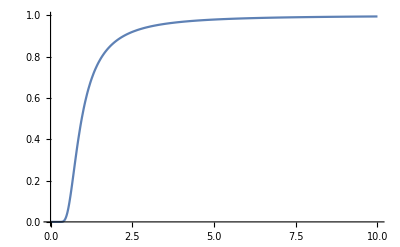

```mathematica
Plot[2/(Exp[1/x^2]+1),{x,0,10},PlotRange->All]
```

```mathematica
Solve[{-1==m x0+b,1==m x1+b},{m,b}]//FullSimplify
```

{{m→2/(-x0+x1),b→(x0+x1)/(x0-x1)}}

```mathematica
Solve[y==m x+b/.{m->2/(-x0+x1),b->(x0+x1)/(x0-x1)},x]//Simplify
```

{{x→1/2 (x0+x1-x0 y+x1 y)}}

```mathematica
(*project[p_,minima_,maxima_]:=Module[{m,b,pn,scale},
m=2/(maxima-minima); b=(maxima+minima)/(maxima-minima);
pn = m p + b;
scale=(minima+maxima)/2+((maxima-minima)/2)Max[Abs[pn]];
Print[scale//N];
(*pn/=Max[Abs[pn]];
(minima+maxima)/2+((maxima-minima)/2)pn*)
p/scale
];*)
project[p_,minima_,maxima_]:=Module[{ratios},
ratios=Abs[p/Table[If[p[[i]]<0,minima[[i]],maxima[[i]]],{i,Length[p]}]];
(*p/ratios[[Ordering[ratios,-1]//First]]*)
(1-10^-3)p/Max[ratios]
];
```

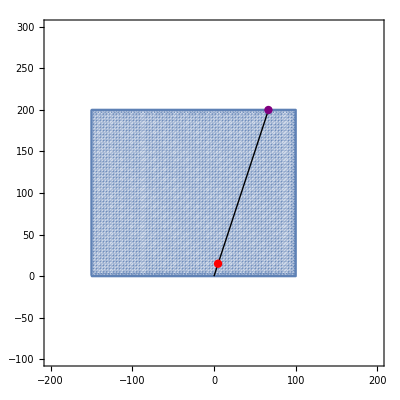

```mathematica
p={5,15};
Show[RegionPlot[0<=T<=200&&-150<=μ<=100,{μ,-200,200},{T,-100,300},PlotPoints->100],Graphics[{Line[{{0,0},p,project[p,{-150,0},{100,200}]}],{Red,PointSize[0.015],Point[p]},{Purple,PointSize[0.015],Point[project[p,{-150,0},{100,200}]]}}],Axes->True]
```

```mathematica
Remove["Global`*"];
ClearAll["Global`*"];
Ndof=1+n+n(n+1)/2//.{n->m+1,m->1}//FullSimplify
pnonc[T_,μB_]:=Sum[Subscript[b, i,j] μB^i T^j,{i,0,2},{j,0,2}]^2/.{Subscript[b, 2,2]->0,Subscript[b, 1,2]->0,Subscript[b, 2,1]->0};
{pnonc[T,μB]==p0,D[pnonc[T,μB],T]==s0,D[pnonc[T,μB],μB]==ρB0,D[pnonc[T,μB],{T,2}]==χTT0,D[pnonc[T,μB],T,μB]==χTμB0,D[pnonc[T,μB],{μB,2}]==χμBμB0}//.{Subscript[b, 0,0]->a,Subscript[b, 1,0]->b,Subscript[b, 0,1]->c,Subscript[b, 0,2]->d,Subscript[b, 1,1]->f,Subscript[b, 2,0]->g}//MatrixForm//FullSimplify
(sol=Solve[{pnonc[T,μB]==p0,D[pnonc[T,μB],T]==s0,D[pnonc[T,μB],μB]==ρB0,D[pnonc[T,μB],{T,2}]==χTT0,D[pnonc[T,μB],T,μB]==χTμB0,D[pnonc[T,μB],{μB,2}]==χμBμB0}//.{Subscript[b, 0,0]->a,Subscript[b, 1,0]->b,Subscript[b, 0,1]->c,Subscript[b, 0,2]->d,Subscript[b, 1,1]->f,Subscript[b, 2,0]->g},{a,b,c,d,f,g}]//FullSimplify//Transpose)//MatrixForm
sol
```

6

(p0==(a+c T+d T^2+μB (b+f T+g μB))^2
s0==2 (c+2 d T+f μB) (a+c T+d T^2+μB (b+f T+g μB))
2 (b+f T+2 g μB) (a+c T+d T^2+μB (b+f T+g μB))==ρB0
2 (c+2 d T+f μB)^2+4 d (a+c T+d T^2+μB (b+f T+g μB))==χTT0
2 (c+2 d T+f μB) (b+f T+2 g μB)+2 f (a+c T+d T^2+μB (b+f T+g μB))==χTμB0
2 (b+f T+2 g μB)^2+4 g (a+c T+d T^2+μB (b+f T+g μB))==χμBμB0)

(a→(-8 p0^2+4 p0 s0 T+(s0 T+μB ρB0)^2-2 p0 (T^2 χTT0+μB (-2 ρB0+2 T χTμB0+μB χμBμB0)))/(8 p0^(3/2)) | a→(8 p0^2-(s0 T+μB ρB0)^2+2 p0 (-2 s0 T+T^2 χTT0+μB (-2 ρB0+2 T χTμB0+μB χμBμB0)))/(8 p0^(3/2))
b→(-ρB0 (s0 T+μB ρB0)+2 p0 (-ρB0+T χTμB0+μB χμBμB0))/(4 p0^(3/2)) | b→(ρB0 (s0 T+μB ρB0)+2 p0 (ρB0-T χTμB0-μB χμBμB0))/(4 p0^(3/2))
c→(-s0 (s0 T+μB ρB0)+2 p0 (-s0+T χTT0+μB χTμB0))/(4 p0^(3/2)) | c→(s0 (s0 T+μB ρB0)+2 p0 (s0-T χTT0-μB χTμB0))/(4 p0^(3/2))
d→(s0^2-2 p0 χTT0)/(8 p0^(3/2)) | d→(-s0^2+2 p0 χTT0)/(8 p0^(3/2))
f→(s0 ρB0-2 p0 χTμB0)/(4 p0^(3/2)) | f→(-s0 ρB0+2 p0 χTμB0)/(4 p0^(3/2))
g→(ρB0^2-2 p0 χμBμB0)/(8 p0^(3/2)) | g→(-ρB0^2+2 p0 χμBμB0)/(8 p0^(3/2)))

{{a→(-8 p0^2+4 p0 s0 T+(s0 T+μB ρB0)^2-2 p0 (T^2 χTT0+μB (-2 ρB0+2 T χTμB0+μB χμBμB0)))/(8 p0^(3/2)),a→(8 p0^2-(s0 T+μB ρB0)^2+2 p0 (-2 s0 T+T^2 χTT0+μB (-2 ρB0+2 T χTμB0+μB χμBμB0)))/(8 p0^(3/2))},{b→(-ρB0 (s0 T+μB ρB0)+2 p0 (-ρB0+T χTμB0+μB χμBμB0))/(4 p0^(3/2)),b→(ρB0 (s0 T+μB ρB0)+2 p0 (ρB0-T χTμB0-μB χμBμB0))/(4 p0^(3/2))},{c→(-s0 (s0 T+μB ρB0)+2 p0 (-s0+T χTT0+μB χTμB0))/(4 p0^(3/2)),c→(s0 (s0 T+μB ρB0)+2 p0 (s0-T χTT0-μB χTμB0))/(4 p0^(3/2))},{d→(s0^2-2 p0 χTT0)/(8 p0^(3/2)),d→(-s0^2+2 p0 χTT0)/(8 p0^(3/2))},{f→(s0 ρB0-2 p0 χTμB0)/(4 p0^(3/2)),f→(-s0 ρB0+2 p0 χTμB0)/(4 p0^(3/2))},{g→(ρB0^2-2 p0 χμBμB0)/(8 p0^(3/2)),g→(-ρB0^2+2 p0 χμBμB0)/(8 p0^(3/2))}}

```mathematica
Sum[Subscript[b, 2i,2j] μB^(2i)T^(2j)If[2(i+j)>4,0,1],{i,0,2},{j,0,2}]
```

b_(0,0)+T^2 b_(0,2)+T^4 b_(0,4)+μB^2 b_(2,0)+T^2 μB^2 b_(2,2)+μB^4 b_(4,0)

```mathematica
Sum[Subscript[b, i,j] μB^i T^j,{i,0,2},{j,0,2}]^2/.{Subscript[b, 2,2]->0,Subscript[b, 1,2]->0,Subscript[b, 2,1]->0}
Sum[Subscript[b, i,j] μB^i T^j If[2(i+j)>4,0,1],{i,0,2},{j,0,2}]^2
```

(b_(0,0)+T b_(0,1)+T^2 b_(0,2)+μB b_(1,0)+T μB b_(1,1)+μB^2 b_(2,0))^2

(b_(0,0)+T b_(0,1)+T^2 b_(0,2)+μB b_(1,0)+T μB b_(1,1)+μB^2 b_(2,0))^2

```mathematica
(*entropy density*)
cfs=DeleteCases[Table[Subscript[b, i,j,k,l] If[2(i+j+k+l)>4,0,1],{i,0,2},{j,0,2},{k,0,2},{l,0,2}]//Flatten,0];
pnonc[T_,μB_,μS_,μQ_]:=Sum[Subscript[b, i,j,k,l] T^i μB^j μS^k μQ^l If[2(i+j+k+l)>4,0,1],{i,0,2},{j,0,2},{k,0,2},{l,0,2}]^2;
eqs={pnonc[T,μB,μS,μQ]==p0,
D[pnonc[T,μB,μS,μQ],T]==s0,
D[pnonc[T,μB,μS,μQ],μB]==ρB0,
D[pnonc[T,μB,μS,μQ],μS]==ρS0,
D[pnonc[T,μB,μS,μQ],μQ]==ρQ0,
D[pnonc[T,μB,μS,μQ],{T,2}]==χTT0,
D[pnonc[T,μB,μS,μQ],T,μB]==χTB0,
D[pnonc[T,μB,μS,μQ],T,μS]==χTS0,
D[pnonc[T,μB,μS,μQ],T,μQ]==χTQ0,
D[pnonc[T,μB,μS,μQ],{μB,2}]==χBB0,
D[pnonc[T,μB,μS,μQ],{μS,2}]==χSS0,
D[pnonc[T,μB,μS,μQ],{μQ,2}]==χQQ0,
D[pnonc[T,μB,μS,μQ],μB,μS]==χBS0,
D[pnonc[T,μB,μS,μQ],μB,μQ]==χBQ0,
D[pnonc[T,μB,μS,μQ],μS,μQ]==χSQ0
};
Length/@{eqs,cfs}
sol=Solve[eqs,cfs]
(sol//FullSimplify//Transpose)//MatrixForm
```

{15,15}

{{b_(0,0,0,0)→1/(2 ρQ0 ρS0-4 p0 χSQ0)(-2 √p0 (ρQ0 ρS0-2 p0 χSQ0)+(s0 T (ρQ0 ρS0-2 p0 χSQ0))/(√p0)+(s0^2 T^2 (ρQ0 ρS0-2 p0 χSQ0))/(4 p0^(3/2))+(μB ρB0 (ρQ0 ρS0-2 p0 χSQ0))/(√p0)+(s0 T μB ρB0 (ρQ0 ρS0-2 p0 χSQ0))/(2 p0^(3/2))+(μB^2 ρB0^2 (ρQ0 ρS0-2 p0 χSQ0))/(4 p0^(3/2))+(μQ ρQ0 (ρQ0 ρS0-2 p0 χSQ0))/(√p0)+(s0 T μQ ρQ0 (ρQ0 ρS0-2 p0 χSQ0))/(2 p0^(3/2))+(μB μQ ρB0 ρQ0 (ρQ0 ρS0-2 p0 χSQ0))/(2 p0^(3/2))+(μQ^2 ρQ0^2 (ρQ0 ρS0-2 p0 χSQ0))/(4 p0^(3/2))+(μS ρS0 (ρQ0 ρS0-2 p0 χSQ0))/(√p0)+(s0 T μS ρS0 (ρQ0 ρS0-2 p0 χSQ0))/(2 p0^(3/2))+(μB μS ρB0 ρS0 (ρQ0 ρS0-2 p0 χSQ0))/(2 p0^(3/2))+(μQ μS ρQ0 ρS0 (ρQ0 ρS0-2 p0 χSQ0))/(2 p0^(3/2))+(μS^2 ρS0^2 (ρQ0 ρS0-2 p0 χSQ0))/(4 p0^(3/2))-(μB^2 χBB0 (ρQ0 ρS0-2 p0 χSQ0))/(2 √p0)-(μB μQ χBQ0 (ρQ0 ρS0-2 p0 χSQ0))/(√p0)-(μB μS χBS0 (ρQ0 ρS0-2 p0 χSQ0))/(√p0)-(μQ^2 χQQ0 (ρQ0 ρS0-2 p0 χSQ0))/(2 √p0)-(μQ μS χSQ0 (ρQ0 ρS0-2 p0 χSQ0))/(√p0)-(μS^2 (ρQ0 ρS0-2 p0 χSQ0) χSS0)/(2 √p0)-(T μB (ρQ0 ρS0-2 p0 χSQ0) χTB0)/(√p0)-(T μQ (ρQ0 ρS0-2 p0 χSQ0) χTQ0)/(√p0)-(T μS (ρQ0 ρS0-2 p0 χSQ0) χTS0)/(√p0)-(T^2 (ρQ0 ρS0-2 p0 χSQ0) χTT0)/(2 √p0)),b_(0,0,0,1)→1/(4 (-ρQ0 ρS0+2 p0 χSQ0))((2 ρQ0^2 ρS0)/(√p0)+(s0 T ρQ0^2 ρS0)/p0^(3/2)+(μB ρB0 ρQ0^2 ρS0)/p0^(3/2)+(μQ ρQ0^3 ρS0)/p0^(3/2)+(μS ρQ0^2 ρS0^2)/p0^(3/2)-(2 μB ρQ0 ρS0 χBQ0)/(√p0)-(2 μQ ρQ0 ρS0 χQQ0)/(√p0)-4 √p0 ρQ0 χSQ0-(2 s0 T ρQ0 χSQ0)/(√p0)-(2 μB ρB0 ρQ0 χSQ0)/(√p0)-(2 μQ ρQ0^2 χSQ0)/(√p0)-(4 μS ρQ0 ρS0 χSQ0)/(√p0)+4 √p0 μB χBQ0 χSQ0+4 √p0 μQ χQQ0 χSQ0+4 √p0 μS χSQ0^2-(2 T ρQ0 ρS0 χTQ0)/(√p0)+4 √p0 T χSQ0 χTQ0),b_(0,0,0,2)→(-(ρQ0^3 ρS0)/p0^(3/2)+(2 ρQ0 ρS0 χQQ0)/(√p0)+(2 ρQ0^2 χSQ0)/(√p0)-4 √p0 χQQ0 χSQ0)/(8 (-ρQ0 ρS0+2 p0 χSQ0)),b_(0,0,1,0)→1/(4 (-ρQ0 ρS0+2 p0 χSQ0))((2 ρQ0 ρS0^2)/(√p0)+(s0 T ρQ0 ρS0^2)/p0^(3/2)+(μB ρB0 ρQ0 ρS0^2)/p0^(3/2)+(μQ ρQ0^2 ρS0^2)/p0^(3/2)+(μS ρQ0 ρS0^3)/p0^(3/2)-(2 μB ρQ0 ρS0 χBS0)/(√p0)-4 √p0 ρS0 χSQ0-(2 s0 T ρS0 χSQ0)/(√p0)-(2 μB ρB0 ρS0 χSQ0)/(√p0)-(4 μQ ρQ0 ρS0 χSQ0)/(√p0)-(2 μS ρS0^2 χSQ0)/(√p0)+4 √p0 μB χBS0 χSQ0+4 √p0 μQ χSQ0^2-(2 μS ρQ0 ρS0 χSS0)/(√p0)+4 √p0 μS χSQ0 χSS0-(2 T ρQ0 ρS0 χTS0)/(√p0)+4 √p0 T χSQ0 χTS0),b_(0,0,1,1)→(ρQ0 ρS0-2 p0 χSQ0)/(4 p0^(3/2)),b_(0,0,2,0)→(-(ρQ0 ρS0^3)/p0^(3/2)+(2 ρS0^2 χSQ0)/(√p0)+(2 ρQ0 ρS0 χSS0)/(√p0)-4 √p0 χSQ0 χSS0)/(8 (-ρQ0 ρS0+2 p0 χSQ0)),b_(0,1,0,0)→1/(4 (-ρQ0 ρS0+2 p0 χSQ0))((2 ρB0 ρQ0 ρS0)/(√p0)+(s0 T ρB0 ρQ0 ρS0)/p0^(3/2)+(μB ρB0^2 ρQ0 ρS0)/p0^(3/2)+(μQ ρB0 ρQ0^2 ρS0)/p0^(3/2)+(μS ρB0 ρQ0 ρS0^2)/p0^(3/2)-(2 μB ρQ0 ρS0 χBB0)/(√p0)-(2 μQ ρQ0 ρS0 χBQ0)/(√p0)-(2 μS ρQ0 ρS0 χBS0)/(√p0)-4 √p0 ρB0 χSQ0-(2 s0 T ρB0 χSQ0)/(√p0)-(2 μB ρB0^2 χSQ0)/(√p0)-(2 μQ ρB0 ρQ0 χSQ0)/(√p0)-(2 μS ρB0 ρS0 χSQ0)/(√p0)+4 √p0 μB χBB0 χSQ0+4 √p0 μQ χBQ0 χSQ0+4 √p0 μS χBS0 χSQ0-(2 T ρQ0 ρS0 χTB0)/(√p0)+4 √p0 T χSQ0 χTB0),b_(0,1,0,1)→(-(ρB0 ρQ0^2 ρS0)/p0^(3/2)+(2 ρQ0 ρS0 χBQ0)/(√p0)+(2 ρB0 ρQ0 χSQ0)/(√p0)-4 √p0 χBQ0 χSQ0)/(4 (-ρQ0 ρS0+2 p0 χSQ0)),b_(0,1,1,0)→(-(ρB0 ρQ0 ρS0^2)/p0^(3/2)+(2 ρQ0 ρS0 χBS0)/(√p0)+(2 ρB0 ρS0 χSQ0)/(√p0)-4 √p0 χBS0 χSQ0)/(4 (-ρQ0 ρS0+2 p0 χSQ0)),b_(0,2,0,0)→(-(ρB0^2 ρQ0 ρS0)/p0^(3/2)+(2 ρQ0 ρS0 χBB0)/(√p0)+(2 ρB0^2 χSQ0)/(√p0)-4 √p0 χBB0 χSQ0)/(8 (-ρQ0 ρS0+2 p0 χSQ0)),b_(1,0,0,0)→1/(4 (-ρQ0 ρS0+2 p0 χSQ0))((2 s0 ρQ0 ρS0)/(√p0)+(s0^2 T ρQ0 ρS0)/p0^(3/2)+(s0 μB ρB0 ρQ0 ρS0)/p0^(3/2)+(s0 μQ ρQ0^2 ρS0)/p0^(3/2)+(s0 μS ρQ0 ρS0^2)/p0^(3/2)-4 √p0 s0 χSQ0-(2 s0^2 T χSQ0)/(√p0)-(2 s0 μB ρB0 χSQ0)/(√p0)-(2 s0 μQ ρQ0 χSQ0)/(√p0)-(2 s0 μS ρS0 χSQ0)/(√p0)-(2 μB ρQ0 ρS0 χTB0)/(√p0)+4 √p0 μB χSQ0 χTB0-(2 μQ ρQ0 ρS0 χTQ0)/(√p0)+4 √p0 μQ χSQ0 χTQ0-(2 μS ρQ0 ρS0 χTS0)/(√p0)+4 √p0 μS χSQ0 χTS0-(2 T ρQ0 ρS0 χTT0)/(√p0)+4 √p0 T χSQ0 χTT0),b_(1,0,0,1)→(-(s0 ρQ0^2 ρS0)/p0^(3/2)+(2 s0 ρQ0 χSQ0)/(√p0)+(2 ρQ0 ρS0 χTQ0)/(√p0)-4 √p0 χSQ0 χTQ0)/(4 (-ρQ0 ρS0+2 p0 χSQ0)),b_(1,0,1,0)→(-(s0 ρQ0 ρS0^2)/p0^(3/2)+(2 s0 ρS0 χSQ0)/(√p0)+(2 ρQ0 ρS0 χTS0)/(√p0)-4 √p0 χSQ0 χTS0)/(4 (-ρQ0 ρS0+2 p0 χSQ0)),b_(1,1,0,0)→(-(s0 ρB0 ρQ0 ρS0)/p0^(3/2)+(2 s0 ρB0 χSQ0)/(√p0)+(2 ρQ0 ρS0 χTB0)/(√p0)-4 √p0 χSQ0 χTB0)/(4 (-ρQ0 ρS0+2 p0 χSQ0)),b_(2,0,0,0)→(-(s0^2 ρQ0 ρS0)/p0^(3/2)+(2 s0^2 χSQ0)/(√p0)+(2 ρQ0 ρS0 χTT0)/(√p0)-4 √p0 χSQ0 χTT0)/(8 (-ρQ0 ρS0+2 p0 χSQ0))},{b_(0,0,0,0)→1/(2 ρQ0 ρS0-4 p0 χSQ0)(-2 √p0 (-ρQ0 ρS0+2 p0 χSQ0)+(s0 T (-ρQ0 ρS0+2 p0 χSQ0))/(√p0)+(s0^2 T^2 (-ρQ0 ρS0+2 p0 χSQ0))/(4 p0^(3/2))+(μB ρB0 (-ρQ0 ρS0+2 p0 χSQ0))/(√p0)+(s0 T μB ρB0 (-ρQ0 ρS0+2 p0 χSQ0))/(2 p0^(3/2))+(μB^2 ρB0^2 (-ρQ0 ρS0+2 p0 χSQ0))/(4 p0^(3/2))+(μQ ρQ0 (-ρQ0 ρS0+2 p0 χSQ0))/(√p0)+(s0 T μQ ρQ0 (-ρQ0 ρS0+2 p0 χSQ0))/(2 p0^(3/2))+(μB μQ ρB0 ρQ0 (-ρQ0 ρS0+2 p0 χSQ0))/(2 p0^(3/2))+(μQ^2 ρQ0^2 (-ρQ0 ρS0+2 p0 χSQ0))/(4 p0^(3/2))+(μS ρS0 (-ρQ0 ρS0+2 p0 χSQ0))/(√p0)+(s0 T μS ρS0 (-ρQ0 ρS0+2 p0 χSQ0))/(2 p0^(3/2))+(μB μS ρB0 ρS0 (-ρQ0 ρS0+2 p0 χSQ0))/(2 p0^(3/2))+(μQ μS ρQ0 ρS0 (-ρQ0 ρS0+2 p0 χSQ0))/(2 p0^(3/2))+(μS^2 ρS0^2 (-ρQ0 ρS0+2 p0 χSQ0))/(4 p0^(3/2))-(μB^2 χBB0 (-ρQ0 ρS0+2 p0 χSQ0))/(2 √p0)-(μB μQ χBQ0 (-ρQ0 ρS0+2 p0 χSQ0))/(√p0)-(μB μS χBS0 (-ρQ0 ρS0+2 p0 χSQ0))/(√p0)-(μQ^2 χQQ0 (-ρQ0 ρS0+2 p0 χSQ0))/(2 √p0)-(μQ μS χSQ0 (-ρQ0 ρS0+2 p0 χSQ0))/(√p0)-(μS^2 (-ρQ0 ρS0+2 p0 χSQ0) χSS0)/(2 √p0)-(T μB (-ρQ0 ρS0+2 p0 χSQ0) χTB0)/(√p0)-(T μQ (-ρQ0 ρS0+2 p0 χSQ0) χTQ0)/(√p0)-(T μS (-ρQ0 ρS0+2 p0 χSQ0) χTS0)/(√p0)-(T^2 (-ρQ0 ρS0+2 p0 χSQ0) χTT0)/(2 √p0)),b_(0,0,0,1)→1/(4 (-ρQ0 ρS0+2 p0 χSQ0))(-(2 ρQ0^2 ρS0)/(√p0)-(s0 T ρQ0^2 ρS0)/p0^(3/2)-(μB ρB0 ρQ0^2 ρS0)/p0^(3/2)-(μQ ρQ0^3 ρS0)/p0^(3/2)-(μS ρQ0^2 ρS0^2)/p0^(3/2)+(2 μB ρQ0 ρS0 χBQ0)/(√p0)+(2 μQ ρQ0 ρS0 χQQ0)/(√p0)+4 √p0 ρQ0 χSQ0+(2 s0 T ρQ0 χSQ0)/(√p0)+(2 μB ρB0 ρQ0 χSQ0)/(√p0)+(2 μQ ρQ0^2 χSQ0)/(√p0)+(4 μS ρQ0 ρS0 χSQ0)/(√p0)-4 √p0 μB χBQ0 χSQ0-4 √p0 μQ χQQ0 χSQ0-4 √p0 μS χSQ0^2+(2 T ρQ0 ρS0 χTQ0)/(√p0)-4 √p0 T χSQ0 χTQ0),b_(0,0,0,2)→((ρQ0^3 ρS0)/p0^(3/2)-(2 ρQ0 ρS0 χQQ0)/(√p0)-(2 ρQ0^2 χSQ0)/(√p0)+4 √p0 χQQ0 χSQ0)/(8 (-ρQ0 ρS0+2 p0 χSQ0)),b_(0,0,1,0)→1/(4 (-ρQ0 ρS0+2 p0 χSQ0))(-(2 ρQ0 ρS0^2)/(√p0)-(s0 T ρQ0 ρS0^2)/p0^(3/2)-(μB ρB0 ρQ0 ρS0^2)/p0^(3/2)-(μQ ρQ0^2 ρS0^2)/p0^(3/2)-(μS ρQ0 ρS0^3)/p0^(3/2)+(2 μB ρQ0 ρS0 χBS0)/(√p0)+4 √p0 ρS0 χSQ0+(2 s0 T ρS0 χSQ0)/(√p0)+(2 μB ρB0 ρS0 χSQ0)/(√p0)+(4 μQ ρQ0 ρS0 χSQ0)/(√p0)+(2 μS ρS0^2 χSQ0)/(√p0)-4 √p0 μB χBS0 χSQ0-4 √p0 μQ χSQ0^2+(2 μS ρQ0 ρS0 χSS0)/(√p0)-4 √p0 μS χSQ0 χSS0+(2 T ρQ0 ρS0 χTS0)/(√p0)-4 √p0 T χSQ0 χTS0),b_(0,0,1,1)→(-ρQ0 ρS0+2 p0 χSQ0)/(4 p0^(3/2)),b_(0,0,2,0)→((ρQ0 ρS0^3)/p0^(3/2)-(2 ρS0^2 χSQ0)/(√p0)-(2 ρQ0 ρS0 χSS0)/(√p0)+4 √p0 χSQ0 χSS0)/(8 (-ρQ0 ρS0+2 p0 χSQ0)),b_(0,1,0,0)→1/(4 (-ρQ0 ρS0+2 p0 χSQ0))(-(2 ρB0 ρQ0 ρS0)/(√p0)-(s0 T ρB0 ρQ0 ρS0)/p0^(3/2)-(μB ρB0^2 ρQ0 ρS0)/p0^(3/2)-(μQ ρB0 ρQ0^2 ρS0)/p0^(3/2)-(μS ρB0 ρQ0 ρS0^2)/p0^(3/2)+(2 μB ρQ0 ρS0 χBB0)/(√p0)+(2 μQ ρQ0 ρS0 χBQ0)/(√p0)+(2 μS ρQ0 ρS0 χBS0)/(√p0)+4 √p0 ρB0 χSQ0+(2 s0 T ρB0 χSQ0)/(√p0)+(2 μB ρB0^2 χSQ0)/(√p0)+(2 μQ ρB0 ρQ0 χSQ0)/(√p0)+(2 μS ρB0 ρS0 χSQ0)/(√p0)-4 √p0 μB χBB0 χSQ0-4 √p0 μQ χBQ0 χSQ0-4 √p0 μS χBS0 χSQ0+(2 T ρQ0 ρS0 χTB0)/(√p0)-4 √p0 T χSQ0 χTB0),b_(0,1,0,1)→((ρB0 ρQ0^2 ρS0)/p0^(3/2)-(2 ρQ0 ρS0 χBQ0)/(√p0)-(2 ρB0 ρQ0 χSQ0)/(√p0)+4 √p0 χBQ0 χSQ0)/(4 (-ρQ0 ρS0+2 p0 χSQ0)),b_(0,1,1,0)→((ρB0 ρQ0 ρS0^2)/p0^(3/2)-(2 ρQ0 ρS0 χBS0)/(√p0)-(2 ρB0 ρS0 χSQ0)/(√p0)+4 √p0 χBS0 χSQ0)/(4 (-ρQ0 ρS0+2 p0 χSQ0)),b_(0,2,0,0)→((ρB0^2 ρQ0 ρS0)/p0^(3/2)-(2 ρQ0 ρS0 χBB0)/(√p0)-(2 ρB0^2 χSQ0)/(√p0)+4 √p0 χBB0 χSQ0)/(8 (-ρQ0 ρS0+2 p0 χSQ0)),b_(1,0,0,0)→1/(4 (-ρQ0 ρS0+2 p0 χSQ0))(-(2 s0 ρQ0 ρS0)/(√p0)-(s0^2 T ρQ0 ρS0)/p0^(3/2)-(s0 μB ρB0 ρQ0 ρS0)/p0^(3/2)-(s0 μQ ρQ0^2 ρS0)/p0^(3/2)-(s0 μS ρQ0 ρS0^2)/p0^(3/2)+4 √p0 s0 χSQ0+(2 s0^2 T χSQ0)/(√p0)+(2 s0 μB ρB0 χSQ0)/(√p0)+(2 s0 μQ ρQ0 χSQ0)/(√p0)+(2 s0 μS ρS0 χSQ0)/(√p0)+(2 μB ρQ0 ρS0 χTB0)/(√p0)-4 √p0 μB χSQ0 χTB0+(2 μQ ρQ0 ρS0 χTQ0)/(√p0)-4 √p0 μQ χSQ0 χTQ0+(2 μS ρQ0 ρS0 χTS0)/(√p0)-4 √p0 μS χSQ0 χTS0+(2 T ρQ0 ρS0 χTT0)/(√p0)-4 √p0 T χSQ0 χTT0),b_(1,0,0,1)→((s0 ρQ0^2 ρS0)/p0^(3/2)-(2 s0 ρQ0 χSQ0)/(√p0)-(2 ρQ0 ρS0 χTQ0)/(√p0)+4 √p0 χSQ0 χTQ0)/(4 (-ρQ0 ρS0+2 p0 χSQ0)),b_(1,0,1,0)→((s0 ρQ0 ρS0^2)/p0^(3/2)-(2 s0 ρS0 χSQ0)/(√p0)-(2 ρQ0 ρS0 χTS0)/(√p0)+4 √p0 χSQ0 χTS0)/(4 (-ρQ0 ρS0+2 p0 χSQ0)),b_(1,1,0,0)→((s0 ρB0 ρQ0 ρS0)/p0^(3/2)-(2 s0 ρB0 χSQ0)/(√p0)-(2 ρQ0 ρS0 χTB0)/(√p0)+4 √p0 χSQ0 χTB0)/(4 (-ρQ0 ρS0+2 p0 χSQ0)),b_(2,0,0,0)→((s0^2 ρQ0 ρS0)/p0^(3/2)-(2 s0^2 χSQ0)/(√p0)-(2 ρQ0 ρS0 χTT0)/(√p0)+4 √p0 χSQ0 χTT0)/(8 (-ρQ0 ρS0+2 p0 χSQ0))}}

(b_(0,0,0,0)→(-8 p0^2+4 p0 s0 T+(s0 T+μB ρB0+μQ ρQ0+μS ρS0)^2-2 p0 (μB^2 χBB0+μQ^2 χQQ0+2 μB (-ρB0+μQ χBQ0+μS χBS0+T χTB0)+2 μQ (-ρQ0+μS χSQ0+T χTQ0)+μS (-2 ρS0+μS χSS0+2 T χTS0)+T^2 χTT0))/(8 p0^(3/2)) | b_(0,0,0,0)→(8 p0^2-(s0 T+μB ρB0+μQ ρQ0+μS ρS0)^2+2 p0 (-2 μS ρS0+μB^2 χBB0+2 μB (-ρB0+μQ χBQ0+μS χBS0)+μQ (-2 ρQ0+μQ χQQ0+2 μS χSQ0)+μS^2 χSS0+T (-2 s0+2 μB χTB0+2 μQ χTQ0+2 μS χTS0+T χTT0)))/(8 p0^(3/2))
b_(0,0,0,1)→(-ρQ0 (s0 T+μB ρB0+μQ ρQ0+μS ρS0)+2 p0 (-ρQ0+μB χBQ0+μQ χQQ0+μS χSQ0+T χTQ0))/(4 p0^(3/2)) | b_(0,0,0,1)→(ρQ0 (s0 T+μB ρB0+μQ ρQ0+μS ρS0)-2 p0 (-ρQ0+μB χBQ0+μQ χQQ0+μS χSQ0+T χTQ0))/(4 p0^(3/2))
b_(0,0,0,2)→(ρQ0^2-2 p0 χQQ0)/(8 p0^(3/2)) | b_(0,0,0,2)→(-ρQ0^2+2 p0 χQQ0)/(8 p0^(3/2))
b_(0,0,1,0)→(-ρS0 (s0 T+μB ρB0+μQ ρQ0+μS ρS0)+2 p0 (-ρS0+μB χBS0+μQ χSQ0+μS χSS0+T χTS0))/(4 p0^(3/2)) | b_(0,0,1,0)→(ρS0 (s0 T+μB ρB0+μQ ρQ0+μS ρS0)-2 p0 (-ρS0+μB χBS0+μQ χSQ0+μS χSS0+T χTS0))/(4 p0^(3/2))
b_(0,0,1,1)→(ρQ0 ρS0-2 p0 χSQ0)/(4 p0^(3/2)) | b_(0,0,1,1)→(-ρQ0 ρS0+2 p0 χSQ0)/(4 p0^(3/2))
b_(0,0,2,0)→(ρS0^2-2 p0 χSS0)/(8 p0^(3/2)) | b_(0,0,2,0)→(-ρS0^2+2 p0 χSS0)/(8 p0^(3/2))
b_(0,1,0,0)→(-ρB0 (s0 T+μB ρB0+μQ ρQ0+μS ρS0)+2 p0 (-ρB0+μB χBB0+μQ χBQ0+μS χBS0+T χTB0))/(4 p0^(3/2)) | b_(0,1,0,0)→(ρB0 (s0 T+μB ρB0+μQ ρQ0+μS ρS0)-2 p0 (-ρB0+μB χBB0+μQ χBQ0+μS χBS0+T χTB0))/(4 p0^(3/2))
b_(0,1,0,1)→(ρB0 ρQ0-2 p0 χBQ0)/(4 p0^(3/2)) | b_(0,1,0,1)→(-ρB0 ρQ0+2 p0 χBQ0)/(4 p0^(3/2))
b_(0,1,1,0)→(ρB0 ρS0-2 p0 χBS0)/(4 p0^(3/2)) | b_(0,1,1,0)→(-ρB0 ρS0+2 p0 χBS0)/(4 p0^(3/2))
b_(0,2,0,0)→(ρB0^2-2 p0 χBB0)/(8 p0^(3/2)) | b_(0,2,0,0)→(-ρB0^2+2 p0 χBB0)/(8 p0^(3/2))
b_(1,0,0,0)→(-s0 (s0 T+μB ρB0+μQ ρQ0+μS ρS0)+2 p0 (-s0+μB χTB0+μQ χTQ0+μS χTS0+T χTT0))/(4 p0^(3/2)) | b_(1,0,0,0)→(s0 (s0 T+μB ρB0+μQ ρQ0+μS ρS0)+2 p0 (s0-μB χTB0-μQ χTQ0-μS χTS0-T χTT0))/(4 p0^(3/2))
b_(1,0,0,1)→(s0 ρQ0-2 p0 χTQ0)/(4 p0^(3/2)) | b_(1,0,0,1)→(-s0 ρQ0+2 p0 χTQ0)/(4 p0^(3/2))
b_(1,0,1,0)→(s0 ρS0-2 p0 χTS0)/(4 p0^(3/2)) | b_(1,0,1,0)→(-s0 ρS0+2 p0 χTS0)/(4 p0^(3/2))
b_(1,1,0,0)→(s0 ρB0-2 p0 χTB0)/(4 p0^(3/2)) | b_(1,1,0,0)→(-s0 ρB0+2 p0 χTB0)/(4 p0^(3/2))
b_(2,0,0,0)→(s0^2-2 p0 χTT0)/(8 p0^(3/2)) | b_(2,0,0,0)→(-s0^2+2 p0 χTT0)/(8 p0^(3/2)))

```mathematica
1/(8 p0^(3/2))(-8 p0^2+(e0+p0)^2-2 p0 (μB^2 χBB0+μQ^2 χQQ0-2(e0+p0)+2 μB (μQ χBQ0+μS χBS0+T χTB0)+2 μQ (μS χSQ0+T χTQ0)+μS (μS χSS0+2 T χTS0)+T^2 χTT0))//FullSimplify
```

```mathematica
tr=(μB^2 χBB0+μQ^2 χQQ0+2 μQ μS χSQ0+μS^2 χSS0+2 μB (μQ χBQ0+μS χBS0+T χTB0)+2 T μQ χTQ0+2 T μS χTS0+T^2 χTT0)
1/(8 p0^(3/2))(e0^2+6 e0 p0-p0 (3 p0+2 tr))
```

```mathematica
μB^2 χBB0+μQ^2 χQQ0+2 μB (-ρB0+μQ χBQ0+μS χBS0+T χTB0)+2 μQ (-ρQ0+μS χSQ0+T χTQ0)+μS (-2 ρS0+μS χSS0+2 T χTS0)+T^2 χTT0//Expand
```

-2 μB ρB0-2 μQ ρQ0-2 μS ρS0+μB^2 χBB0+2 μB μQ χBQ0+2 μB μS χBS0+μQ^2 χQQ0+2 μQ μS χSQ0+μS^2 χSS0+2 T μB χTB0+2 T μQ χTQ0+2 T μS χTS0+T^2 χTT0

```mathematica
(-ρQ0 (s0 T+μB ρB0+μQ ρQ0+μS ρS0)+2 p0 (-ρQ0+μB χBQ0+μQ χQQ0+μS χSQ0+T χTQ0))/(4 p0^(3/2))
(-ρQ0 (e0+p0)+2 p0 (-ρQ0+μB χBQ0+μQ χQQ0+μS χSQ0+T χTQ0))/(4 p0^(3/2))//FullSimplify
```

(-ρQ0 (s0 T+μB ρB0+μQ ρQ0+μS ρS0)+2 p0 (-ρQ0+μB χBQ0+μQ χQQ0+μS χSQ0+T χTQ0))/(4 p0^(3/2))

(-e0 ρQ0-3 p0 ρQ0+2 p0 (μB χBQ0+μQ χQQ0+μS χSQ0+T χTQ0))/(4 p0^(3/2))

```mathematica
Sum[Subscript[b, i,j,k,l] T^i μB^j μS^k μQ^l If[2(i+j+k+l)>4,0,1],{i,0,2},{j,0,2},{k,0,2},{l,0,2}]//FullSimplify
```

b_(0,0,0,0)+μQ b_(0,0,0,1)+μQ^2 b_(0,0,0,2)+μS b_(0,0,1,0)+μQ μS b_(0,0,1,1)+μS^2 b_(0,0,2,0)+μB b_(0,1,0,0)+μB μQ b_(0,1,0,1)+μB μS b_(0,1,1,0)+μB^2 b_(0,2,0,0)+T b_(1,0,0,0)+T μQ b_(1,0,0,1)+T μS b_(1,0,1,0)+T μB b_(1,1,0,0)+T^2 b_(2,0,0,0)

```mathematica
{pnonc[T,μB,μS,μQ],
D[pnonc[T,μB,μS,μQ],T],
D[pnonc[T,μB,μS,μQ],μB],
D[pnonc[T,μB,μS,μQ],μS],
D[pnonc[T,μB,μS,μQ],μQ],
D[pnonc[T,μB,μS,μQ],{T,2}],
D[pnonc[T,μB,μS,μQ],T,μB],
D[pnonc[T,μB,μS,μQ],T,μS],
D[pnonc[T,μB,μS,μQ],T,μQ],
D[pnonc[T,μB,μS,μQ],{μB,2}],
D[pnonc[T,μB,μS,μQ],{μS,2}],
D[pnonc[T,μB,μS,μQ],{μQ,2}],
D[pnonc[T,μB,μS,μQ],μB,μS],
D[pnonc[T,μB,μS,μQ],μB,μQ],
D[pnonc[T,μB,μS,μQ],μS,μQ]
}/.{Subscript[b, 0,0,0,0]->x-(μQ Subscript[b, 0,0,0,1]+μQ^2 Subscript[b, 0,0,0,2]+μS Subscript[b, 0,0,1,0]+μQ μS Subscript[b, 0,0,1,1]+μS^2 Subscript[b, 0,0,2,0]+μB Subscript[b, 0,1,0,0]+μB μQ Subscript[b, 0,1,0,1]+μB μS Subscript[b, 0,1,1,0]+μB^2 Subscript[b, 0,2,0,0]+T Subscript[b, 1,0,0,0]+T μQ Subscript[b, 1,0,0,1]+T μS Subscript[b, 1,0,1,0]+T μB Subscript[b, 1,1,0,0]+T^2 Subscript[b, 2,0,0,0])}//FullSimplify
```

{x^2,2 x (b_(1,0,0,0)+μQ b_(1,0,0,1)+μS b_(1,0,1,0)+μB b_(1,1,0,0)+2 T b_(2,0,0,0)),2 x (b_(0,1,0,0)+μQ b_(0,1,0,1)+μS b_(0,1,1,0)+2 μB b_(0,2,0,0)+T b_(1,1,0,0)),2 x (b_(0,0,1,0)+μQ b_(0,0,1,1)+2 μS b_(0,0,2,0)+μB b_(0,1,1,0)+T b_(1,0,1,0)),2 x (b_(0,0,0,1)+2 μQ b_(0,0,0,2)+μS b_(0,0,1,1)+μB b_(0,1,0,1)+T b_(1,0,0,1)),4 x b_(2,0,0,0)+2 (b_(1,0,0,0)+μQ b_(1,0,0,1)+μS b_(1,0,1,0)+μB b_(1,1,0,0)+2 T b_(2,0,0,0))^2,2 x b_(1,1,0,0)+2 (b_(0,1,0,0)+μQ b_(0,1,0,1)+μS b_(0,1,1,0)+2 μB b_(0,2,0,0)+T b_(1,1,0,0)) (b_(1,0,0,0)+μQ b_(1,0,0,1)+μS b_(1,0,1,0)+μB b_(1,1,0,0)+2 T b_(2,0,0,0)),2 x b_(1,0,1,0)+2 (b_(0,0,1,0)+μQ b_(0,0,1,1)+2 μS b_(0,0,2,0)+μB b_(0,1,1,0)+T b_(1,0,1,0)) (b_(1,0,0,0)+μQ b_(1,0,0,1)+μS b_(1,0,1,0)+μB b_(1,1,0,0)+2 T b_(2,0,0,0)),2 x b_(1,0,0,1)+2 (b_(0,0,0,1)+2 μQ b_(0,0,0,2)+μS b_(0,0,1,1)+μB b_(0,1,0,1)+T b_(1,0,0,1)) (b_(1,0,0,0)+μQ b_(1,0,0,1)+μS b_(1,0,1,0)+μB b_(1,1,0,0)+2 T b_(2,0,0,0)),4 x b_(0,2,0,0)+2 (b_(0,1,0,0)+μQ b_(0,1,0,1)+μS b_(0,1,1,0)+2 μB b_(0,2,0,0)+T b_(1,1,0,0))^2,4 x b_(0,0,2,0)+2 (b_(0,0,1,0)+μQ b_(0,0,1,1)+2 μS b_(0,0,2,0)+μB b_(0,1,1,0)+T b_(1,0,1,0))^2,4 x b_(0,0,0,2)+2 (b_(0,0,0,1)+2 μQ b_(0,0,0,2)+μS b_(0,0,1,1)+μB b_(0,1,0,1)+T b_(1,0,0,1))^2,2 x b_(0,1,1,0)+2 (b_(0,0,1,0)+μQ b_(0,0,1,1)+2 μS b_(0,0,2,0)+μB b_(0,1,1,0)+T b_(1,0,1,0)) (b_(0,1,0,0)+μQ b_(0,1,0,1)+μS b_(0,1,1,0)+2 μB b_(0,2,0,0)+T b_(1,1,0,0)),2 x b_(0,1,0,1)+2 (b_(0,0,0,1)+2 μQ b_(0,0,0,2)+μS b_(0,0,1,1)+μB b_(0,1,0,1)+T b_(1,0,0,1)) (b_(0,1,0,0)+μQ b_(0,1,0,1)+μS b_(0,1,1,0)+2 μB b_(0,2,0,0)+T b_(1,1,0,0)),2 x b_(0,0,1,1)+2 (b_(0,0,0,1)+2 μQ b_(0,0,0,2)+μS b_(0,0,1,1)+μB b_(0,1,0,1)+T b_(1,0,0,1)) (b_(0,0,1,0)+μQ b_(0,0,1,1)+2 μS b_(0,0,2,0)+μB b_(0,1,1,0)+T b_(1,0,1,0))}